```mathematica
k[x_] = Exp[-(x+.25)^2/2];
p[x_] =Exp[-Abs[x]^1.7];
dlp[x_]=-1.7*Abs[x]^0.7
xi[x_] = dlp[x]*k[x]+D[k[x],x]
p1=Plot[{k[x],dlp[x]},{x,-1,1},PlotLegends->{k[x,t],"∂_x log(p(x))"}]
Export["/home/kcx/dev/mcmc/write_up/presentation/img/kp.pdf",p1]
p1=Plot[{k[x],dlp[x],xi[x]},{x,-1,1},PlotLegends->{k[x,t],"∂_x log(p(x))",Subscript[ξ, p][x,t]}]
Export["/home/kcx/dev/mcmc/write_up/presentation/img/xi.pdf",p1]
```

-1.7 Abs[x]^0.7

ⅇ^(-1/2 (0.25+x)^2) (-0.25-x)-1.7 ⅇ^(-1/2 (0.25+x)^2) Abs[x]^0.7

```mathematica
Simplify[ⅇ^(-1/2 (0.25+x)^2) (-0.25-x)-1.7 ⅇ^(-1/2 (0.25+x)^2) Abs[x]^0.7]
```

ⅇ^(-0.5 (0.25+x)^2) (-0.25-1. x-1.7 Abs[x]^0.7)

```mathematica
k[x_,y_] = Exp[-(x-y)^2/2];
h[x_,y_] = dlp[x]*dlp[y]*k[x,y] + dlp[x]*D[k[x,y],y]+dlp[y]*D[k[x,y],x]+D[D[k[x,y],x],y];
p1=Plot3D[h[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
-Graphics3D-
Export["/home/kcx/dev/mcmc/write_up/presentation/img/h.pdf",p1]
```

-Graphics3D-

/home/kcx/dev/mcmc/write_up/presentation/img/h.pdf

(ⅇ^(-1/2 (-1+x)^2))'+ⅇ^(-1/2 (-1+x)^2) Log[ⅇ^(-Abs[x]^1.7)]'

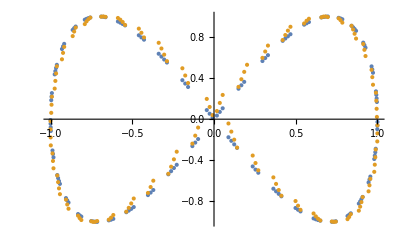

```mathematica
ListPlot[{Table[{Sin[n],Sin[2 n]},{n,150}],Table[{Sin[n],Sin[2.001n]},{n,151}]}]
```

16 Sin[t]^3

13 Cos[t]-4 Cos[2 t]-2 Cos[3 t]-Cos[4 t]

14 Cos[t]-4 Cos[2 t]-2 Cos[3 t]-Cos[4 t]

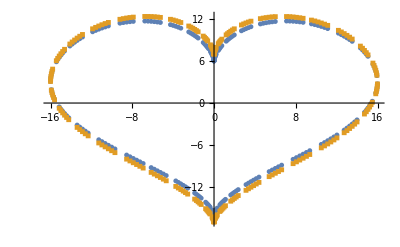

/home/kcx/dev/gatsby_kernels/random_features_testing/post/img2/mostImportant.pdf

```mathematica
x[t_] = 16*Sin[t]^3
y[t_] = 13*Cos[t] - 4*Cos[2*t] - 2*Cos[3*t]-Cos[4*t]
y2[t_] = 14*Cos[t] - 4*Cos[2*t] - 2*Cos[3*t]-Cos[4*t]

p1= ListPlot[{Table[{x[n],y[n]},{n,251}],Table[{x[n],y2[n]},{n,250}]},PlotMarkers->{ Automatic,5}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/post/img2/mostImportant.pdf",p1]
```

```mathematica
p[t_] = Sinc[t/2]^2/(2*Pi);
q[t_] = Sinc[t]^2/(Pi);
Fp[x_]= FourierTransform[p[t],t,x];
Fq[x_]= FourierTransform[q[t],t,x];
Integrate[p[t],{t,-Infinity,Infinity}]
Integrate[q[t],{t,-Infinity,Infinity}]
```

1

1

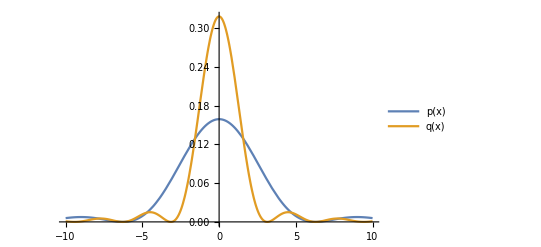

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/density.pdf

```mathematica
p1=Plot[{p[x],q[x]},{x,-10,10},PlotLegends->"Expressions"]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/density.pdf",p1]
```

```mathematica
Fp[0]
```

1/(√(2 π))

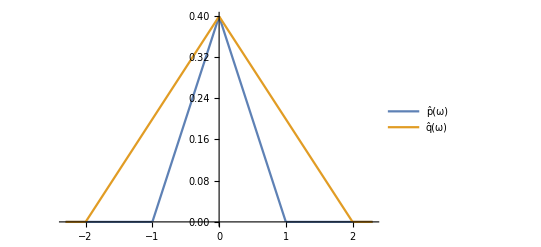

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/fourier.pdf

```mathematica
p2= Plot[{Fp[x],Fq[x]},{x,-2.3,2.3},PlotLegends->{OverHat[p][ω],OverHat[q] [ω]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/fourier.pdf",p2]
```

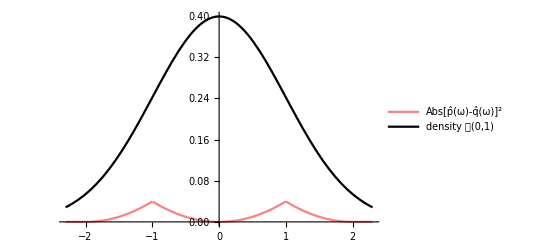

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/difference.pdf

```mathematica
p3=Plot[{Abs[Fp[x]-Fq[x]]^2,1/Sqrt[2*Pi]*Exp[-x^2/2]},{x,-2.3,2.3},PlotStyle->{Pink,Black},PlotLegends->{Abs[OverHat[p][ω]-OverHat[q] [ω]]^2,  𝒩[0,1] density}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/difference.pdf",p3]
```

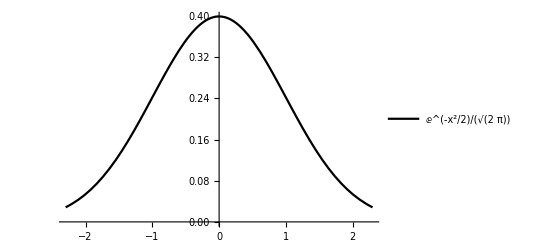

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/gaus.pdf

```mathematica
p4 = Plot[1/Sqrt[2*Pi]*Exp[-x^2/2],{x,-2.3,2.3},PlotLegends->{1/Sqrt[2*Pi]*Exp[-x^2/2]},PlotStyle->{Black}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/gaus.pdf",p4]
```

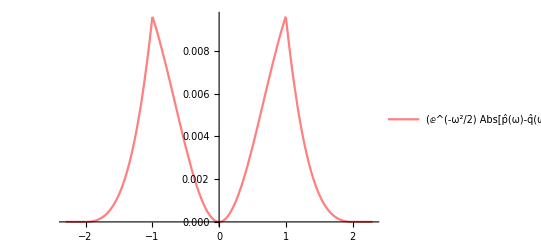

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/product.pdf

```mathematica
p5 = Plot[Abs[Fp[x]-Fq[x]]^2*1/Sqrt[2*Pi]*Exp[-x^2/2],{x,-2.3,2.3},PlotStyle->{Pink},PlotLegends->{Abs[OverHat[p][ω]-OverHat[q][ω]]^2*1/Sqrt[2*Pi]*Exp[-ω^2/2]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/product.pdf",p5]
```

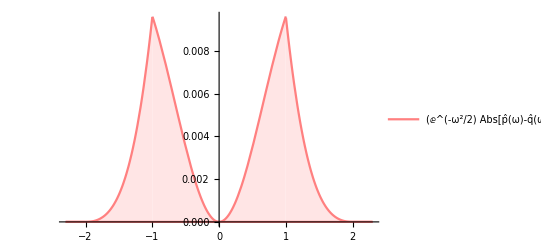

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/integral.pdf

```mathematica
p6 = Plot[{0,Abs[(Fp[x]-Fq[x])]^2*1/Sqrt[2*Pi]*Exp[-x^2/2]},{x,-2.3,2.3},PlotStyle->{Pink},Filling->{1->{2}},PlotLegends->{Abs[OverHat[p][ω]-OverHat[q][ω]]^2*1/Sqrt[2*Pi]*Exp[-ω^2/2]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/integral.pdf",p6]
```

```mathematica
a=0.1232
```

0.1232

```mathematica
line=Function[a, Line[{{a,Min[Fp[a],Fq[a]]},{a,Max[Fp[a],Fq[a]]}}] ];
lineF2=Function[a, Line[{{a,0},{a,1}}] ];
line1 = line[0.2123];
line2 = line [-1.234];
line11 = lineF2[0.2123];
line21 = lineF2[-1.234];
```

Function[a,Line[{{a,Min[Fp[a],Fq[a]]},{a,Max[Fp[a],Fq[a]]}}]]

Function[a,Line[{{a,0},{a,1}}]]

Line[{{0.2123,0.314247},{0.2123,0.356595}}]

Line[{{-1.234,0.},{-1.234,0.152795}}]

Line[{{0.2123,0},{0.2123,1}}]

Line[{{-1.234,0},{-1.234,1}}]

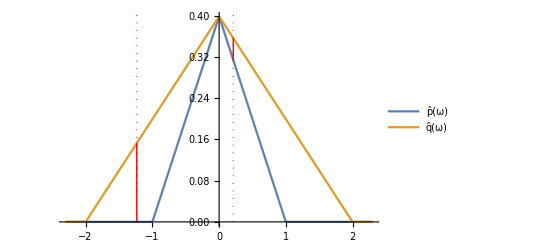

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/freq.pdf

```mathematica
lineStyle={Red};
plt=Plot[{Fp[x],Fq[x]},{x,-2.3,2.3},PlotStyle->{Automatic,Automatic},Epilog->{Directive[lineStyle],line1,line2,Dotted,line11,line21,Thick,line1,line2 },PlotLegends->{OverHat[p][ω],OverHat[q][ω],x1}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/freq.pdf",plt]
```

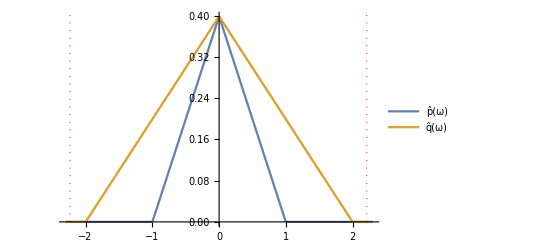

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/badFreq.pdf

```mathematica
line1a = line[2.2123];
line2a = line [-2.234];
line11a = lineF2[2.2123];
line21a = lineF2[-2.234];
plt = Plot[{Fp[x],Fq[x]},{x,-2.3,2.3},PlotStyle->{Automatic,Automatic},Epilog->{Directive[lineStyle],line1a,line2a,Dotted,line11a,line21a,Thick,line1a,line2a },PlotLegends->{OverHat[p][ω],OverHat[q][ω],x1}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/badFreq.pdf",plt]
```

```mathematica
k[x_,y_] = 1/Sqrt[2*Pi]*Exp[-(x-y)^2/2]
```

(ⅇ^(-1/2 (x-y)^2))/(√(2 π))

```mathematica
gft[w_] = FourierTransform[1/Sqrt[2*Pi]*Exp[-x^2/2],x,w]
```

(ⅇ^(-w^2/2))/(√(2 π))

```mathematica
mp[w_]=Simplify[InverseFourierTransform[gft[y]*Fp[y],y,w]]
mq[w_]=Simplify[InverseFourierTransform[gft[y]*Fq[y],y,w]]
```

(ⅇ^(-w^2/2) (√(2 π) (1-ⅈ w) Erf[(1-ⅈ w)/(√2)]+√(2 π) (1+ⅈ w) Erf[(1+ⅈ w)/(√2)]+2 (-2 ⅇ^(w^2/2)+ⅇ^(1/2 (-ⅈ+w)^2)+ⅇ^(1/2 (ⅈ+w)^2)+√(2 π) w Erfi[w/(√2)])))/(4 √2 π^(3/2))

(ⅇ^(-w^2/2) (√(2 π) (2-ⅈ w) Erf[(2-ⅈ w)/(√2)]+√(2 π) (2+ⅈ w) Erf[(2+ⅈ w)/(√2)]+2 (-2 ⅇ^(w^2/2)+ⅇ^(1/2 (-2 ⅈ+w)^2)+ⅇ^(1/2 (2 ⅈ+w)^2)+√(2 π) w Erfi[w/(√2)])))/(8 √2 π^(3/2))

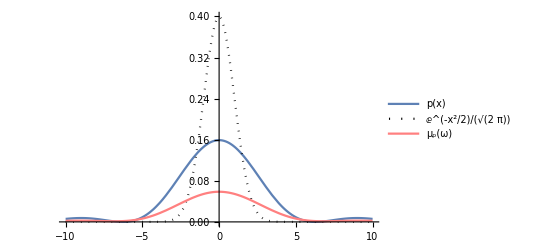

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/meanEmbCreation.pdf

```mathematica
plt =Plot[{p[x],gft[x],mp[x]},{x,-10,10},PlotRange->{0,0.4},PlotStyle->{Automatic,{Black,Dotted},Pink},PlotLegends->{"p(x)",k[x,0],Subscript[μ, p][ω]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/meanEmbCreation.pdf",plt]
```

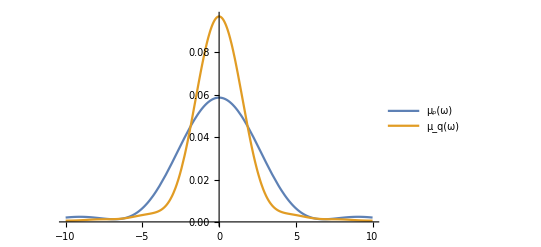

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/meanEmb.pdf

```mathematica
plt =Plot[{mp[x],mq[x]},{x,-10,10},PlotLegends->{Subscript[μ, p][ω],Subscript[μ, q][ω]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/meanEmb.pdf",plt]
```

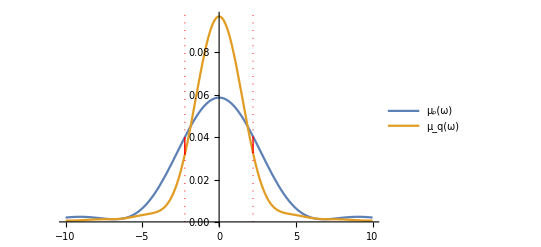

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/Meanfreq.pdf

```mathematica
mline=Function[a, Line[{{a,Min[mp[a],mq[a]]},{a,Max[mp[a],mq[a]]}}] ];
mlineF2=Function[a, Line[{{a,0},{a,1}}] ];
mline1 = mline[2.2123];
mline2 = mline [-2.234];
mline11 = mlineF2[2.2123];
mline21 = mlineF2[-2.234];
plt=Plot[{mp[x],mq[x]},{x,-10,10},PlotStyle->{Automatic,Automatic},Epilog->{Directive[lineStyle],mline1,mline2,Dotted,mline11,mline21,Thick,mline1,mline2 },PlotLegends->{Subscript[μ, p][ω],Subscript[μ, q][ω]}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/Meanfreq.pdf",plt]
```

```mathematica
mean[t_] = Integrate[k[t,x]*Exp[-x^2/2]*1/Sqrt[2*Pi],{x,-Infinity,Infinity}]
```

(ⅇ^(-t^2/4))/(2 √(2 π))

```mathematica
variance[t_]=Integrate[(k[t,x]-k[t,y])^2*Exp[-x^2/2]*1/Sqrt[2*Pi]*Exp[-y^2/2]*1/Sqrt[2*Pi],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

(ⅇ^(-t^2/2) (-3+2 √3 ⅇ^(t^2/6)))/(12 π)

```mathematica
m=500;
empMean1[t_]=Mean[Map[Function[x,k[t,x]],RandomVariate[NormalDistribution[],m]]];
empMean2[t_]=Mean[Map[Function[x,k[t,x]],RandomVariate[NormalDistribution[],m]]];
```

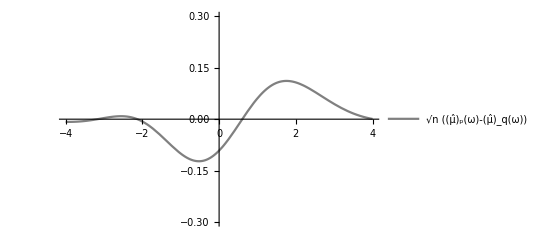

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/justempiricalMean.pdf

```mathematica
plt=Plot[{(empMean1[t]-empMean2[t])*Sqrt[m]},{t,-4,4},PlotRange->{-0.3,0.3},PlotStyle->{Gray},PlotLegends->{ Sqrt[n](Subscript[OverHat[ μ], p][ω]-Subscript[OverHat[μ], q][ω]) } ]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/justempiricalMean.pdf",plt]
```

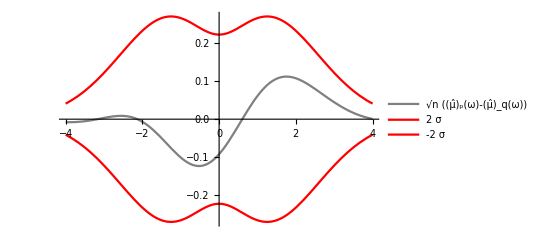

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMean.pdf

```mathematica
plt=Plot[{(empMean1[t]-empMean2[t])*Sqrt[m],2*Sqrt[variance[t]],-2*Sqrt[variance[t]]},{t,-4,4},PlotStyle->{Gray,Red,Red},PlotLegends->{ Sqrt[n](Subscript[OverHat[ μ], p][ω]-Subscript[OverHat[μ], q][ω]) ,2σ,-2σ} ]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMean.pdf",plt]
```

```mathematica
theline=Line[{{2.14,-1},{2.14,1}}]
```

Line[{{2.14,-1},{2.14,1}}]

```mathematica
Line[{{2.14,-1},{2.14,1}}]
```

Line[{{2.14,-1},{2.14,1}}]

```mathematica
Line[{{2.14,-1},{2.14,1}}]
```

Line[{{2.14,-1},{2.14,1}}]

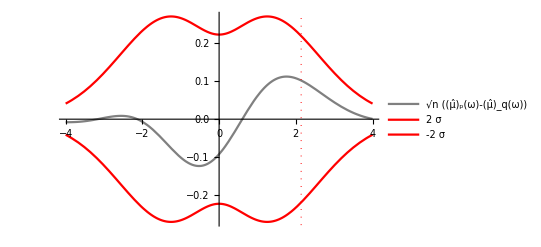

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMeanFreq.pdf

```mathematica
plt=Plot[{(empMean1[t]-empMean2[t])*Sqrt[m],2*Sqrt[variance[t]],-2*Sqrt[variance[t]]},{t,-4,4},PlotStyle->{Gray,Red,Red},PlotLegends->{ Sqrt[n](Subscript[OverHat[ μ], p][ω]-Subscript[OverHat[μ], q][ω]) ,2σ,-2σ},Epilog->{Red,Dotted,theline}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMeanFreq.pdf",plt]
```

```mathematica
empMean3[t_]=Mean[Map[Function[x,k[t,x]],RandomVariate[NormalDistribution[0,2],m]]];
```

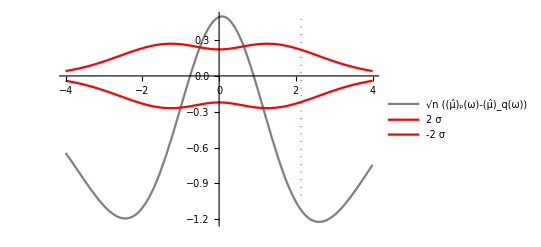

/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMeanFreqAlt.pdf

```mathematica
plt=Plot[{(empMean1[t]-empMean3[t])*Sqrt[m],2*Sqrt[variance[t]],-2*Sqrt[variance[t]]},{t,-4,4},PlotStyle->{Gray,Red,Red},PlotLegends->{ Sqrt[n](Subscript[OverHat[ μ], p][ω]-Subscript[OverHat[μ], q][ω]) ,2σ,-2σ},Epilog->{Red,Dotted,theline}]
Export["/home/kcx/dev/gatsby_kernels/random_features_testing/presentation/img/empiricalMeanFreqAlt.pdf",plt]
```

```mathematica
Integrate[Exp[-(x-z)^2/2 -(y-z)^2/2 -z^2/2 ],{z,-Infinity,Infinity}]
```

ⅇ^(1/3 (-x^2+x y-y^2)) √((2 π)/3)